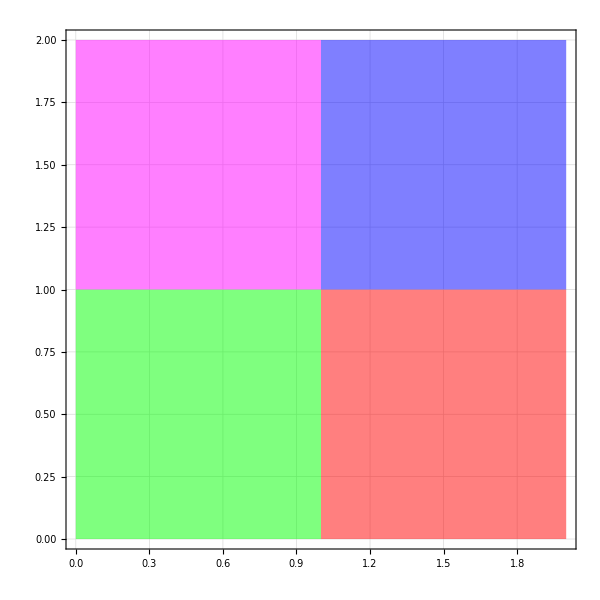

```mathematica
aaa=Graphics[{Red,Opacity[0.5],Rectangle[{1,0}],Blue, Rectangle[{1,1}],Frame->True}];
bbb=Graphics[{Green,Opacity[0.5],Rectangle[{0,0}],Magenta, Rectangle[{0,1}],Frame-> True}];

Show[aaa,bbb,Axes->True,Frame->True,GridLines->Automatic,AspectRatio->1,ImageSize->600]
```

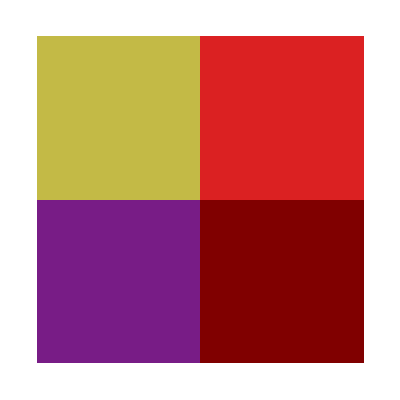

```mathematica
ArrayPlot[{{0.5,0.6},{0.3,{1,2}}},ColorFunction->"Rainbow"]
```

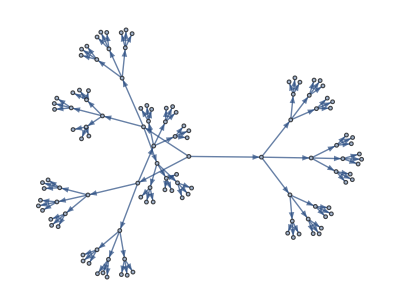

-Graphics-

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
NestGraph[{f[#],g[#],h[#]}&,x,4]
CommunityGraphPlot[RandomGraph[{100,200}]]
```

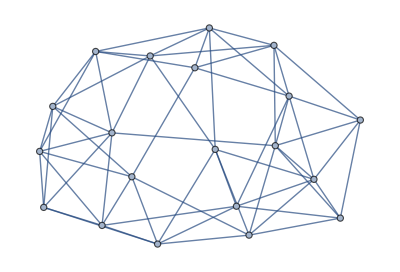

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
RandomGraph[WattsStrogatzGraphDistribution[20,0.3,3]]
```

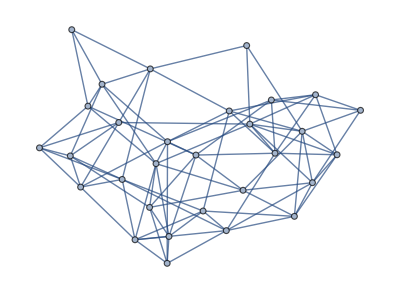

-Graphics-

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
RandomGraph[WattsStrogatzGraphDistribution[30,0.3,3]]
CommunityGraphPlot[%,FindGraphCommunities[%]]
```

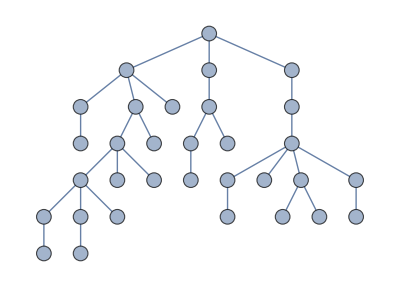

```mathematica
g=TreeGraph[RandomInteger[#]<->#+1&/@Range[0,30],VertexSize->0.4]
```

```mathematica
FindVertexEccentricityPath[g_?UndirectedGraphQ,u_]/;MemberQ[VertexList[g],u]:=Module[{d=GraphDistanceMatrix[g],v,posu,posv,vl=VertexList[g]},posu=VertexIndex[g,u];
posv=First@First@Position[d[[posu]],Max[d[[posu]]]];
PathGraph[FindShortestPath[g,u,vl[[posv]]]]]
```

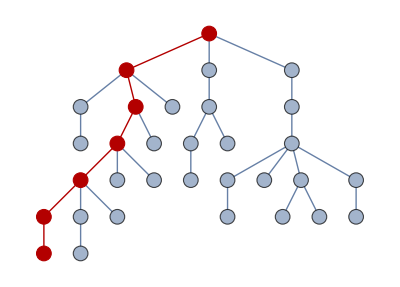
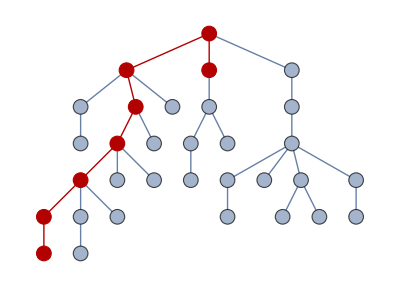
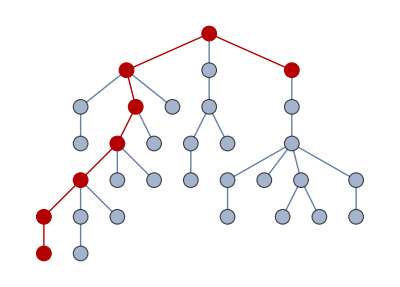

```mathematica
Table[HighlightGraph[g,FindVertexEccentricityPath[g,u]],{u,Range[3]}]
```

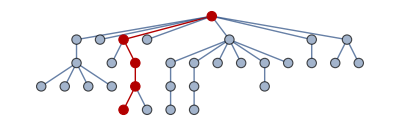
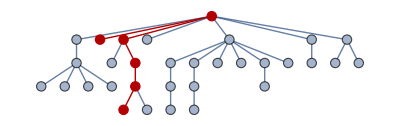
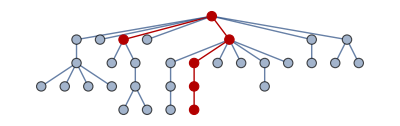

### 简单一点的

```mathematica
findRadiusPath[g_?UndirectedGraphQ]:=Module[{c=First@GraphCenter[g],d,v,pos},d=Table[GraphDistance[g,c,u],{u,VertexList[g]}];
pos=First@Position[d,Max[d]];
v=First@Part[VertexList[g],pos];
PathGraph@FindShortestPath[g,c,v]]
```

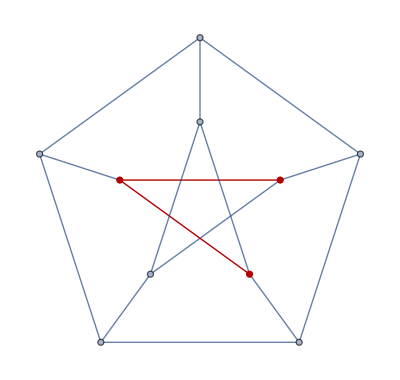
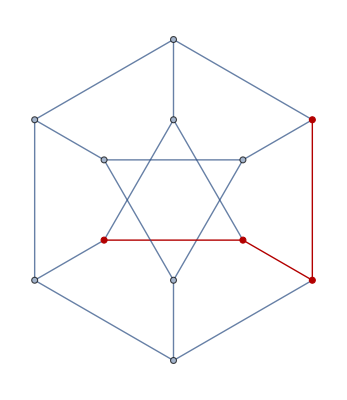

```mathematica
HighlightGraph[#,findRadiusPath[#]]&/@{PetersenGraph[5,2],PetersenGraph[6,2]}
```

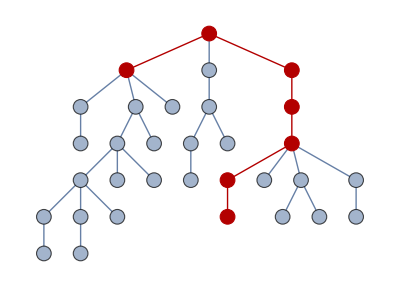

```mathematica
HighlightGraph[g,findRadiusPath[g]]
```

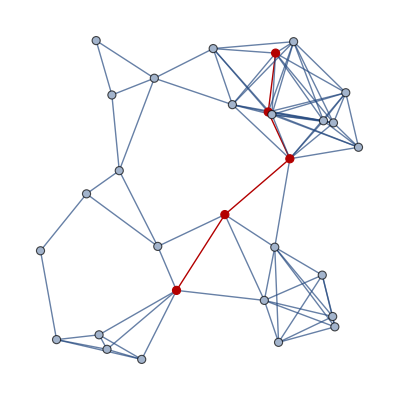

```mathematica
gr = NearestNeighborGraph[RandomReal[1,{30,2}],{All,0.3}];
HighlightGraph[gr,findRadiusPath[gr]]
```

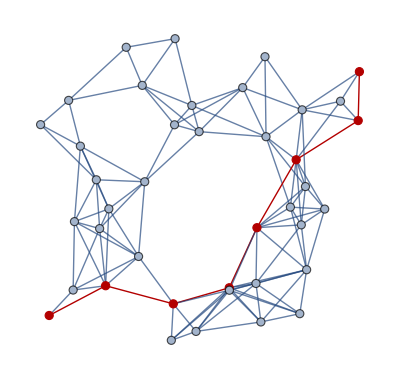

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
FindDiameterPath[g_?UndirectedGraphQ]:=Module[{d=GraphDistanceMatrix[g],u,v,pos},pos=First@Position[d,Max[d]];
{u,v}=Part[VertexList[g],pos];
PathGraph[FindShortestPath[g,u,v]]];
gr = NearestNeighborGraph[RandomReal[1,{40,2}],{All,0.25}];
HighlightGraph[gr,FindDiameterPath[gr]]
```

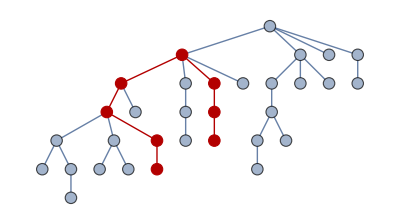

```mathematica
g=TreeGraph[RandomInteger[#]<->#+1&/@Range[0,30],VertexSize->0.4];
FindShortestPath[g,18,28];
HighlightGraph[g,PathGraph[%]]
```

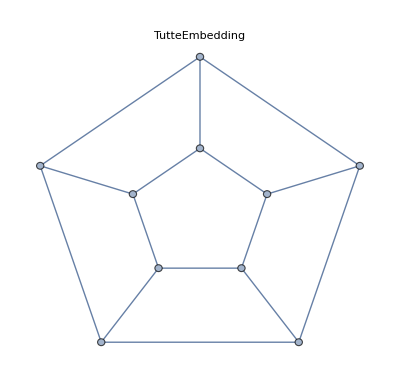
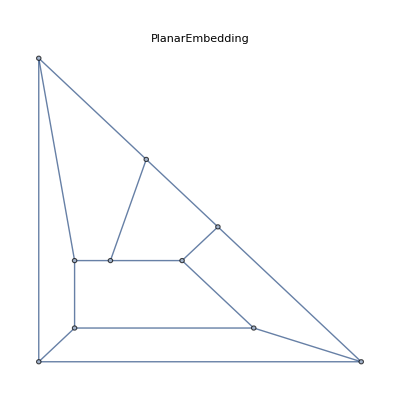

```mathematica
Table[PlanarGraph[{1<->2,1<->5,1<->6,2<->3,2<->7,3<->4,3<->8,4<->5,4<->9,5<->10,6<->7,6<->10,7<->8,8<->9,9<->10},GraphLayout->l,PlotLabel->l],{l,{"TutteEmbedding","PlanarEmbedding"}}]
```

```mathematica
NearestNeighborGraph[RandomReal[1,{50,3}]]
```

-Graphics3D-

```mathematica
CayleyGraph[AbelianGroup[{2,2,2,2}]]
```

-Graphics-

```mathematica
CayleyGraph[AbelianGroup[{2,2,2,2,2}]]
```

-Graphics-

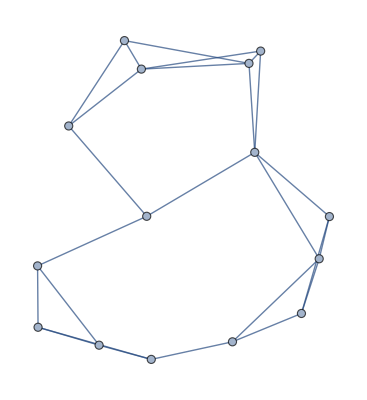

```mathematica
RandomGraph[SpatialGraphDistribution[15,0.35],1]
```

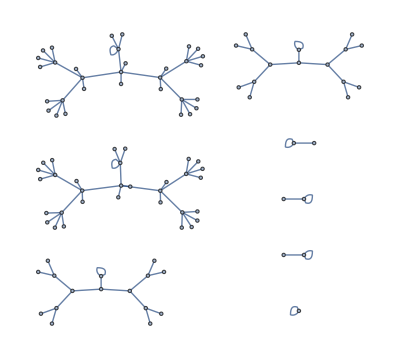

```mathematica
GraphPlot[Table[i->Mod[i^2,102],{i,0,102}]]
```

```mathematica
Table[i->j,{i,6},{j,6}]
```

{{1→1,1→2,1→3,1→4,1→5,1→6},{2→1,2→2,2→3,2→4,2→5,2→6},{3→1,3→2,3→3,3→4,3→5,3→6},{4→1,4→2,4→3,4→4,4→5,4→6},{5→1,5→2,5→3,5→4,5→5,5→6},{6→1,6→2,6→3,6→4,6→5,6→6}}

```mathematica
Flatten[Table[i->j,{i,6},{j,6}]]
```

{1→1,1→2,1→3,1→4,1→5,1→6,2→1,2→2,2→3,2→4,2→5,2→6,3→1,3→2,3→3,3→4,3→5,3→6,4→1,4→2,4→3,4→4,4→5,4→6,5→1,5→2,5→3,5→4,5→5,5→6,6→1,6→2,6→3,6→4,6→5,6→6}

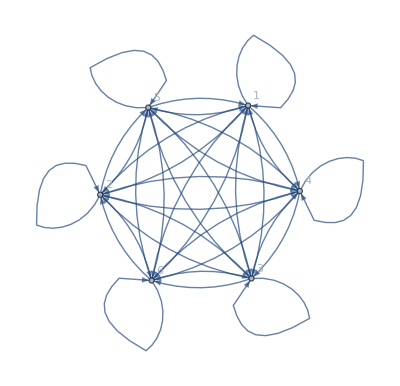

```mathematica
Graph[Flatten[Table[i->j,{i,6},{j,6}]],VertexLabels->"Name"]
```

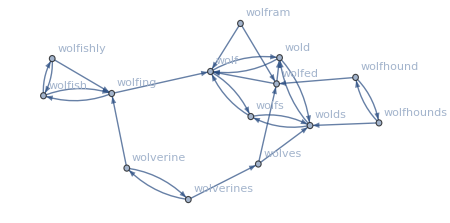

```mathematica
words=DictionaryLookup["wol*"];
Flatten[Map[(Thread[#->DeleteCases[Nearest[words,#,3],#]])&,words]];
Graph[%,VertexLabels->"Name",ImageSize->450]
```

```mathematica
work1={a->b->c->d->g->h};
work2={a->b->v,b->v};
read1={e->c->v->l->w};
read2={j->k->l->w};
read3={q->r->s->t};
play1={s->u};
play2={m->n->a};
sleep1={a->p};
sleep2={w->l->v->c->d->e};
sleep3={a->n->q->r};
```

```mathematica
Subsets[{a,b,c,d,g,h},{2}]
```

{{a,b},{a,c},{a,d},{a,g},{a,h},{b,c},{b,d},{b,g},{b,h},{c,d},{c,g},{c,h},{d,g},{d,h},{g,h}}

```mathematica
kk=Flatten[{work1,work2,read1,read2,read3,sleep1,sleep2,sleep3}]
```

{a→b→c→d→g→h,a→b→v,b→v,e→c→v→l→w,j→k→l→w,q→r→s→t,a→p,w→l→v→c→d→e,a→n→q→r}

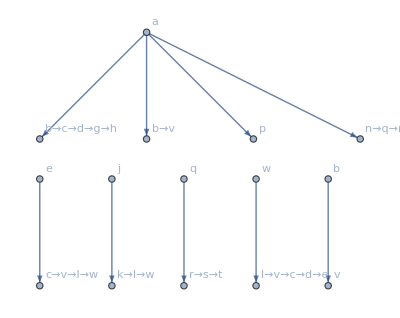

```mathematica
Graph[kk,VertexLabels->"Name"]
```

```mathematica
work1={a->b->c->d->g->h,b->c->d->g->h,c->d->g->h,d->g->h,g->h };
work2={a->b->v,v->b};
read1={e->c->v->l->w,c->v->l->w,v->l->w,l->w};
read2={j->k->l->w,k->l->w,l->w};
read3={q->r->s->t,r->s->t,s->t};
play1={s->u};
play2={m->n->a,n->a};
sleep1={a->p};
sleep2={w->l->v->c->d->e,l->v->c->d->e,v->c->d->e,c->d->e,d->e};
sleep3={a->n->q->r,n->q->r,q->r};
```

```mathematica
kk=Flatten[{work1,work2,read1,read2,read3,sleep1,sleep2,sleep3}]
```

```mathematica
{a->b,b->c,c->d,d->g,g->h,b->c->d->g->h,c->d->g->h,d->g->h,g->h,a->b->v,v->b,e->c->v->l->w,c->v->l->w,v->l->w,l->w,j->k->l->w,k->l->w,l->w,q->r->s->t,r->s->t,s->t,a->p,w->l->v->c->d->e,l->v->c->d->e,v->c->d->e,c->d->e,d->e,a->n->q->r,n->q->r,q->r}
```

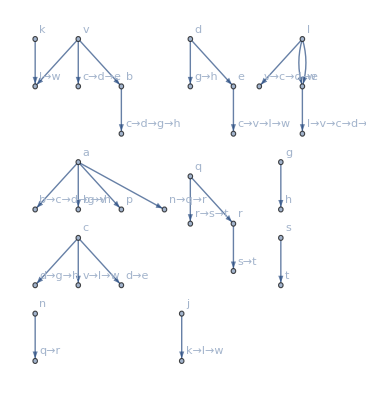

```mathematica
Graph[kk,VertexLabels->"Name"]
```

```mathematica
Rule@@@Partition[Characters["antidisestablishmentarianism"],2,1]
```

{a→n,n→t,t→i,i→d,d→i,i→s,s→e,e→s,s→t,t→a,a→b,b→l,l→i,i→s,s→h,h→m,m→e,e→n,n→t,t→a,a→r,r→i,i→a,a→n,n→i,i→s,s→m}

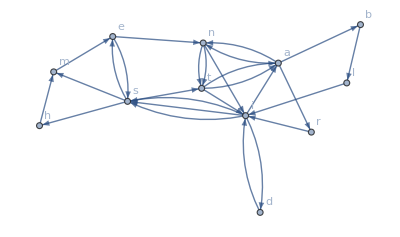

```mathematica
Graph[Rule@@@Partition[Characters["antidisestablishmentarianism"],2,1],VertexLabels->All]
```

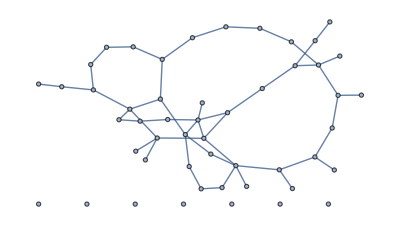

```mathematica
v=myRandomGraph = RandomGraph[{50,50}, VertexSize->Automatic]
```

```mathematica
gr = NearestNeighborGraph[v,{All,1}, VertexCoordinates->v]
```

NearestNeighborGraph::list: List expected at position 1 in ….

NearestNeighborGraph[-Graphics-,{All,1},VertexCoordinates→-Graphics-]